## PROTON TO ROPER TFF DATA 15/03/2017

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Mo16data:=ErrorListPlot[{{{0.649999976,0.0674641803},ErrorBar[0.01751679]},{{0.949999988,0.0762328506},ErrorBar[0.0176014826]},{{1.29999995,0.095839642},ErrorBar[0.019425964]}},Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,PlotStyle->{Directive[Darker[Black,0.4]],AbsolutePointSize[7],AbsoluteThickness[2]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->12}]
```

```mathematica
Mo12data:=ErrorListPlot[{{{0.316885,0.0543},ErrorBar[0.01226]},{{0.373472,0.0587},ErrorBar[0.00914]},{{0.430059,0.0592},ErrorBar[0.01055]},{{0.486646,0.0642},ErrorBar[0.00798]},{{0.543232,0.0789},ErrorBar[0.01248]},{{0.599819,0.0641},ErrorBar[0.00857]},{{0.656406,0.0562},ErrorBar[0.01549]}},
Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,PlotStyle->{Directive[Darker[Green,0.4]],AbsolutePointSize[7],AbsoluteThickness[2]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->12}]
```

```mathematica
Az09data:=ErrorListPlot[{{{0.325211,0.0554529},ErrorBar[0.006793]},{{0.437557,0.0579482},ErrorBar[0.0069316]},{{0.549902,0.0718115},ErrorBar[0.0090111]},{{0.715464,0.0754159},ErrorBar[0.0106747]},{{0.999285,0.0903882},ErrorBar[0.0133088]},{{1.93352,0.107024},ErrorBar[0.0134472]},{{2.30604,0.0945471},ErrorBar[0.0130316]},{{2.74951,0.0679298},ErrorBar[0.0099815]},{{3.28758,0.0585028},ErrorBar[0.007902]},{{3.92618,0.0451941},ErrorBar[0.0102588]},{{4.69486,0.0418669},ErrorBar[0.0112293]}},Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,Axes->False,PlotStyle->{Directive[Darker[Red,0.2]],AbsolutePointSize[7],AbsoluteThickness[2]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Courier",FontSize->12}]
```

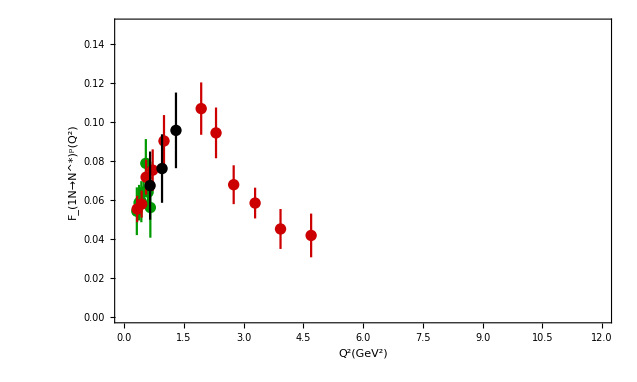

```mathematica
gpTFF=Show[Mo12data,Az09data,Mo16data,PlotRange->{{0,12},{0,0.15}},AspectRatio->0.6,FrameLabel->{"Q^2(GeV^2)","F_(1N→N^*)^p(Q^2)"}]
```